{{377,798}}

C:\Users\Расим\Desktop\Курсовая\test\dl.txt

(0.398942 ⅇ^(-(-b+x)^2/(2 c^2)))/d

{d→0.000188948,b→785.893,c→84.1336}

Function[{t},2111.38 ⅇ^(-0.0000706367 (-785.893+x)^2)]

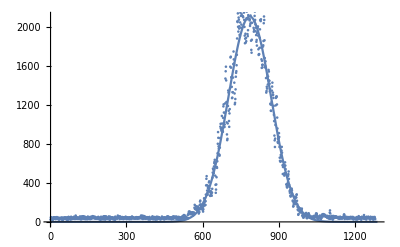

```mathematica
a=Import["C:\\Users\\Расим\\Desktop\\Курсовая\\test\\beam_00000005.pgm","Table"];
pos=Position[a,Max[a]]
(*For[i=0,i<1280,i++,If[a[[379,i]]>1357,Print[a[[379,i]]]]];*)
(*Position[a,1570];*)
(*Max[a];*)
data=a[[pos[[1,1]],All]];
Export["C:\\Users\\Расим\\Desktop\\Курсовая\\test\\dl.txt", data]
model=Exp[-(x-b)^2/(2c^2)]/(d*(2*Pi)^(0.5))
fit=FindFit[data,model,{d,b,c},x]
modelf=Function[{t},Evaluate[model/.fit]]
Show[Plot[modelf[x],{x,1,1289}], ListPlot[a[[pos[[1,1]],All]]]]
```

```mathematica
Show[%7,AxesLabel->{RawBoxes[RowBox[{"Длина",",",RowBox[{"усл",".","ед","."}]}]],RawBoxes[RowBox[{"Амплитуда",",",RowBox[{"усл",".","ед","."}]}]]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Function is not a type of graphics.

Show[Function[{t},2111.38 ⅇ^(-0.0000706367 (-785.893+x)^2)],AxesLabel→{Длина,усл.ед.,Амплитуда,усл.ед.},PlotLabel→None,LabelStyle→{GrayLevel[0]}]

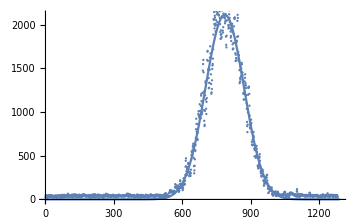

```mathematica
Show[%8,ImageSize->Medium]
```

```mathematica
Show[%9,ImageSize->Large]
```

Show::gtype: Function is not a type of graphics.

Show::gtype: Show is not a type of graphics.

Show[Show[Function[{t},2111.38 ⅇ^(-0.0000706367 (-785.893+x)^2)],AxesLabel→{Длина,усл.ед.,Амплитуда,усл.ед.},PlotLabel→None,LabelStyle→{GrayLevel[0]}],ImageSize→Large]

C:\Users\Расим\Desktop\Курсовая\dlina_file_5.jpg

C:\Users\Расим\Desktop\Курсовая\dlina_file_5.jpg

C:\Users\Расим\Desktop\Курсовая\dlina_file_5.jpg

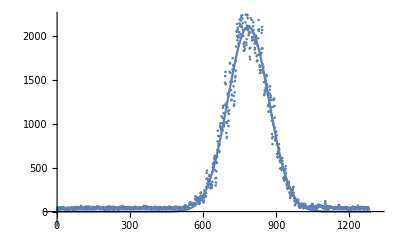

```mathematica
Export["C:\\Users\\Расим\\Desktop\\Курсовая\\dlina_file_5.jpg",%10,"JPEG"]
```